# Sample Option Example

This example reuses Tutorial part 1. At the end we show how to modify the “Sample” method options

## Unmodified beginning of the Tutorial 1

```mathematica
<< CmdStan`
```

```mathematica
SetDirectory[$TemporaryDirectory]
```

/tmp

```mathematica
stanCode="data
{
  int<lower = 0> N;
  vector[N] x;
  vector[N] y;
}
parameters
{
  real alpha;
  real beta;
  real<lower = 0> sigma;
}
model {
  y ~normal(alpha + beta * x, sigma);
}";
```

```mathematica
stanExeFile = CompileStanCode[stanCodeFile,StanVerbose->False]
```

/tmp/linear_regression

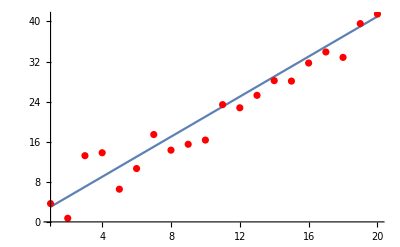

```mathematica
σ=3;α=1;β=2;
n=20;
X=Range[n];
Y=α+β*X+RandomVariate[NormalDistribution[0,σ],n];
p=Show[Plot[α+β*x,{x,Min[X],Max[X]}],ListPlot[Transpose@{X,Y},PlotStyle->Red]]
```

```mathematica
stanData=<|"N"->n,"x"->X,"y"->Y|>;
stanDataFile=ExportStanData[stanExeFile,stanData]
```

/tmp/linear_regression.data.R

## Option modification example

A run with sample default options

```mathematica
stanResultFile=RunStan[stanExeFile,SampleDefaultOptions]
```

Running: /tmp/linear_regression method=sample data file=/tmp/linear_regression.data.R output file=/tmp/linear_regression.csv

method = sample (Default)
  sample
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default)
    save_warmup = 0 (Default)
    thin = 1 (Default)
    adapt
      engaged = 1 (Default)
      gamma = 0.050000000000000003 (Default)
      delta = 0.80000000000000004 (Default)
      kappa = 0.75 (Default)
      t0 = 10 (Default)
      init_buffer = 75 (Default)
      term_buffer = 50 (Default)
      window = 25 (Default)
    algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
            max_depth = 10 (Default)
        metric = diag_e (Default)
        metric_file =  (Default)
        stepsize = 1 (Default)
        stepsize_jitter = 0 (Default)
id = 0 (Default)
data
  file = /tmp/linear_regression.data.R
init = 2 (Default)
random
  seed = 3714706817 (Default)
output
  file = /tmp/linear_regression.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)
  sig_figs = -1 (Default)
stanc_version = stanc3 b25c0b64
stancflags = 


Gradient evaluation took 1.2e-05 seconds
1000 transitions using 10 leapfrog steps per transition would take 0.12 seconds.
Adjust your expectations accordingly!


Iteration:    1 / 2000 [  0%]  (Warmup)
Iteration:  100 / 2000 [  5%]  (Warmup)
Iteration:  200 / 2000 [ 10%]  (Warmup)
Iteration:  300 / 2000 [ 15%]  (Warmup)
Iteration:  400 / 2000 [ 20%]  (Warmup)
Iteration:  500 / 2000 [ 25%]  (Warmup)
Iteration:  600 / 2000 [ 30%]  (Warmup)
Iteration:  700 / 2000 [ 35%]  (Warmup)
Iteration:  800 / 2000 [ 40%]  (Warmup)
Iteration:  900 / 2000 [ 45%]  (Warmup)
Iteration: 1000 / 2000 [ 50%]  (Warmup)
Iteration: 1001 / 2000 [ 50%]  (Sampling)
Iteration: 1100 / 2000 [ 55%]  (Sampling)
Iteration: 1200 / 2000 [ 60%]  (Sampling)
Iteration: 1300 / 2000 [ 65%]  (Sampling)
Iteration: 1400 / 2000 [ 70%]  (Sampling)
Iteration: 1500 / 2000 [ 75%]  (Sampling)
Iteration: 1600 / 2000 [ 80%]  (Sampling)
Iteration: 1700 / 2000 [ 85%]  (Sampling)
Iteration: 1800 / 2000 [ 90%]  (Sampling)
Iteration: 1900 / 2000 [ 95%]  (Sampling)
Iteration: 2000 / 2000 [100%]  (Sampling)

 Elapsed Time: 0.045 seconds (Warm-up)
               0.057 seconds (Sampling)
               0.102 seconds (Total)

/tmp/linear_regression.csv

Now with customized option values

Note: 

you can see available options looking at previous command output or by reading CmdStan manual
https://mc-stan.org/docs/2_24/cmdstan-guide-2_24.pdf

by example we will modify MCMC options:
    num_samples = 1000 (Default)
    num_warmup = 1000 (Default) 
    
  and
  
   algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
            max_depth = 10 (Default)

#### Copy default Sample option

```mathematica
myOpt=SampleDefaultOptions
```

method=sample

#### Modify some values

```mathematica
myOpt=SetStanOption[myOpt,"adapt.num_samples",2000]
myOpt=SetStanOption[myOpt,"adapt.num_warmup",1500]
myOpt=SetStanOption[myOpt,"algorithm=hmc.engine=nuts.max_depth",5]
```

method=sample adapt num_samples=2000 num_warmup=1500 algorithm=hmc engine=nuts max_depth=5

method=sample adapt num_samples=2000 num_warmup=1500 algorithm=hmc engine=nuts max_depth=5

method=sample adapt num_samples=2000 num_warmup=1500 algorithm=hmc engine=nuts max_depth=5

#### Perform a new run with these options

```mathematica
stanResultFile=RunStan[stanExeFile,myOpt]
```

Running: /tmp/linear_regression method=sample adapt num_samples=2000 num_warmup=1500 algorithm=hmc engine=nuts max_depth=5 data file=/tmp/linear_regression.data.R output file=/tmp/linear_regression.csv

method = sample (Default)
  sample
    num_samples = 2000
    num_warmup = 1500
    save_warmup = 0 (Default)
    thin = 1 (Default)
    adapt
      engaged = 1 (Default)
      gamma = 0.050000000000000003 (Default)
      delta = 0.80000000000000004 (Default)
      kappa = 0.75 (Default)
      t0 = 10 (Default)
      init_buffer = 75 (Default)
      term_buffer = 50 (Default)
      window = 25 (Default)
    algorithm = hmc (Default)
      hmc
        engine = nuts (Default)
          nuts
            max_depth = 5
        metric = diag_e (Default)
        metric_file =  (Default)
        stepsize = 1 (Default)
        stepsize_jitter = 0 (Default)
id = 0 (Default)
data
  file = /tmp/linear_regression.data.R
init = 2 (Default)
random
  seed = 3720771451 (Default)
output
  file = /tmp/linear_regression.csv
  diagnostic_file =  (Default)
  refresh = 100 (Default)
  sig_figs = -1 (Default)
stanc_version = stanc3 b25c0b64
stancflags = 


Gradient evaluation took 1.3e-05 seconds
1000 transitions using 10 leapfrog steps per transition would take 0.13 seconds.
Adjust your expectations accordingly!


Iteration:    1 / 3500 [  0%]  (Warmup)
Iteration:  100 / 3500 [  2%]  (Warmup)
Iteration:  200 / 3500 [  5%]  (Warmup)
Iteration:  300 / 3500 [  8%]  (Warmup)
Iteration:  400 / 3500 [ 11%]  (Warmup)
Iteration:  500 / 3500 [ 14%]  (Warmup)
Iteration:  600 / 3500 [ 17%]  (Warmup)
Iteration:  700 / 3500 [ 20%]  (Warmup)
Iteration:  800 / 3500 [ 22%]  (Warmup)
Iteration:  900 / 3500 [ 25%]  (Warmup)
Iteration: 1000 / 3500 [ 28%]  (Warmup)
Iteration: 1100 / 3500 [ 31%]  (Warmup)
Iteration: 1200 / 3500 [ 34%]  (Warmup)
Iteration: 1300 / 3500 [ 37%]  (Warmup)
Iteration: 1400 / 3500 [ 40%]  (Warmup)
Iteration: 1500 / 3500 [ 42%]  (Warmup)
Iteration: 1501 / 3500 [ 42%]  (Sampling)
Iteration: 1600 / 3500 [ 45%]  (Sampling)
Iteration: 1700 / 3500 [ 48%]  (Sampling)
Iteration: 1800 / 3500 [ 51%]  (Sampling)
Iteration: 1900 / 3500 [ 54%]  (Sampling)
Iteration: 2000 / 3500 [ 57%]  (Sampling)
Iteration: 2100 / 3500 [ 60%]  (Sampling)
Iteration: 2200 / 3500 [ 62%]  (Sampling)
Iteration: 2300 / 3500 [ 65%]  (Sampling)
Iteration: 2400 / 3500 [ 68%]  (Sampling)
Iteration: 2500 / 3500 [ 71%]  (Sampling)
Iteration: 2600 / 3500 [ 74%]  (Sampling)
Iteration: 2700 / 3500 [ 77%]  (Sampling)
Iteration: 2800 / 3500 [ 80%]  (Sampling)
Iteration: 2900 / 3500 [ 82%]  (Sampling)
Iteration: 3000 / 3500 [ 85%]  (Sampling)
Iteration: 3100 / 3500 [ 88%]  (Sampling)
Iteration: 3200 / 3500 [ 91%]  (Sampling)
Iteration: 3300 / 3500 [ 94%]  (Sampling)
Iteration: 3400 / 3500 [ 97%]  (Sampling)
Iteration: 3500 / 3500 [100%]  (Sampling)

 Elapsed Time: 0.053 seconds (Warm-up)
               0.094 seconds (Sampling)
               0.147 seconds (Total)

/tmp/linear_regression.csv

### Read back option values

```mathematica
GetStanOption[myOpt,"adapt.num_warmup"]
GetStanOption[myOpt,"algorithm=hmc.engine=nuts.max_depth"]
```

1500

5

### Remove the preivously customized “max_depth” value

```mathematica
myOpt=RemoveStanOption[myOpt,"algorithm=hmc.engine=nuts.max_depth"]
```

method=sample adapt num_samples=2000 num_warmup=1500